```mathematica
ClearAll[x,y]
DSolve[
{I*D[Cos[x[t]]*Exp[I*y[t]],t]== g*Cos[x[t]]*Sin[x[t]]*Sin[x[t]]*Exp[I*y[t]],
I*D[Sin[x[t]]*Exp[-I*y[t]],t]== g*Sin[x[t]]*Cos[x[t]]*Cos[x[t]]*Exp[-I*y[t]]},
{x[t],y[t]},t,Assumptions->{x[t],y[t]}∈Reals]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{x[t]→1/2 ArcSin[ⅇ^(-ⅈ t+C[1])],y[t]→-(-ⅈ+ⅈ ⅇ^(-2 ⅈ t+2 C[1]))/(2 √(1-ⅇ^(-2 ⅈ t+2 C[1])))+C[2]}}

```mathematica
FullSimplify[Out[7]]
```

```mathematica
{{x[t]->1/2 ArcSin[ⅇ^(-ⅈ g t+C[1])],y[t]->1/2 ⅈ √(1-ⅇ^(-2 ⅈ g t+2 C[1]))+C[2]}}
```

```mathematica
g=1
```

1

```mathematica
x[t_]=1/2ArcSin[Exp[-I*g*t]]
y[t_]=(I/2)(Sqrt[1-Exp[-2*I*g*t]]-1)
```

1/2 ArcSin[ⅇ^(-ⅈ t)]

1/2 ⅈ (-1+√(1-ⅇ^(-2 ⅈ t)))

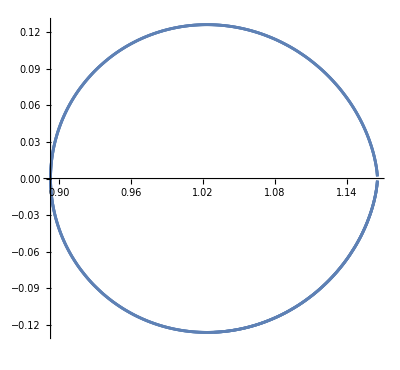

```mathematica
p1 = ParametricPlot[ReIm[Cos[x[t]]Exp[I*y[t]]],{t,0,10}]
```

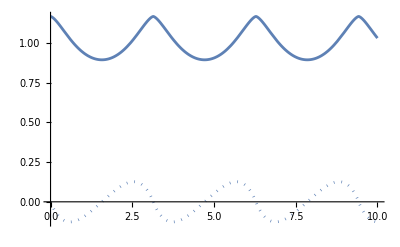

```mathematica
ReImPlot[Cos[x[t]]Exp[I*y[t]],{t,0,10}]
```

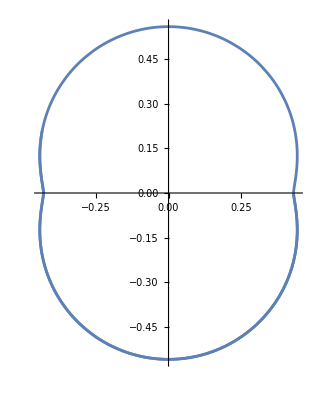

```mathematica
p2 = ParametricPlot[ReIm[Sin[x[t]]Exp[-I*y[t]]],{t,0,10}]
```

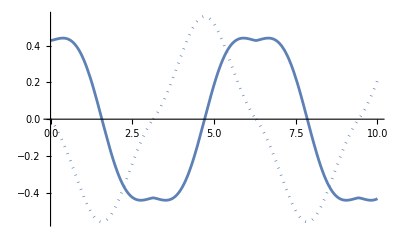

```mathematica
ReImPlot[Sin[x[t]]Exp[-I*y[t]],{t,0,10}]
```

```mathematica
Show[p1,p2]
```

-Graphics-